```mathematica
f=x^2+2x^3Exp[x]
```

x^2+2 ⅇ^x x^3

```mathematica
D[f,x]
D[D[f,x],x]
```

2 x+6 ⅇ^x x^2+2 ⅇ^x x^3

2+12 ⅇ^x x+12 ⅇ^x x^2+2 ⅇ^x x^3

```mathematica
D[f, {x,2}]
```

2+12 ⅇ^x x+12 ⅇ^x x^2+2 ⅇ^x x^3

```mathematica
f/.x->2
```

4+16 ⅇ^2

```mathematica
g= 1/(1+x^2)
```

1/(1+x^2)

```mathematica
h=Integrate[g,x]
```

ArcTan[x]

```mathematica
(h/.x->1)-(h/.x->0)
```

π/4

```mathematica
Integrate[1/(1+x^2), {x,0,1}]
```

π/4

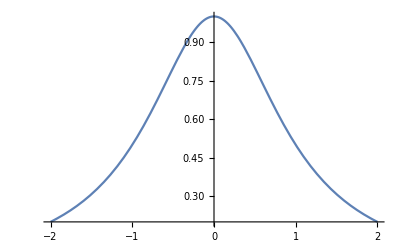

```mathematica
Plot[g, {x,-2,2}]
```

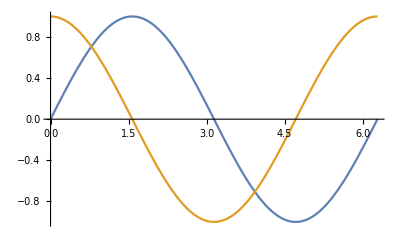

```mathematica
Plot[{Sin[x], Cos[x]}, {x,0,2Pi}]
```

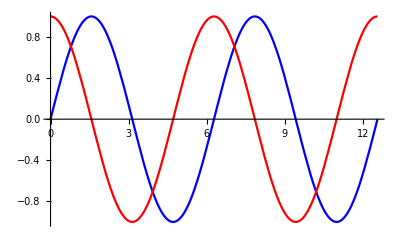

```mathematica
Plot[{Sin[x], Cos[x]}, {x,0,4Pi}, PlotStyle->{Blue, Red}]
```

```mathematica
Clear[f]
```

```mathematica
f[x_] := x Exp[-x^2]
```

```mathematica
Function[x,x Exp[-x^2]]
```

Function[x,x Exp[-x^2]]

```mathematica
f[1]
```

1/ⅇ

```mathematica
D[f[x],x]
```

ⅇ^(-x^2)-2 ⅇ^(-x^2) x^2

```mathematica
f'[x]
```

ⅇ^(-x^2)-2 ⅇ^(-x^2) x^2

```mathematica
f''[x]
```

-6 ⅇ^(-x^2) x+4 ⅇ^(-x^2) x^3

```mathematica
f''[2]
```

20/ⅇ^4

```mathematica
Integrate[f[x],x]
```

-(ⅇ^(-x^2))/2